```mathematica
SetDirectory@NotebookDirectory[]
```

/home/eric/git/nonlinear-systems-lab/Project 1

```mathematica
rawdata=Import["data/raw/final_heavy_death1.tsv"]
```

{{time,1,2,3,4},{1465.39,,,125.5,},{1465.39,,,,547},{1465.39,,202.25,,},{1465.41,,,125.5,},{1465.41,,,,547},9981,{1525.61,418.75,,,},{1525.63,,,95,},{1525.63,,,,518},{1525.63,418.75,,,},{1525.63,,208.75,,}}
 |  |  |  |

```mathematica
tagDist=.396;
pivotFromTag =tagDist*0.26582;
pendulumlen = 0.335;
```

# Unify timestamps

```mathematica
preprocess[rawdata_]:=Module[{(*header,gathered,data,meandist, x,x1,x2,θ1,θ2*)},
header=ToString/@rawdata[[1]];
gathered=Gather[rawdata[[2;;All]],First[#1]==First[#2]&];
data=Transpose[Mean[Select[#,NumberQ]]&/@Transpose[#]&/@gathered];
meandist = Mean[Select[data[[5]]-data[[4]],NumberQ]];
(*Print[meandist];*)

(* Convert to meters *)
data[[2;;All]]= data[[2;;All]]*tagDist/meandist;

x=Mean[{data[[4]],data[[5]]-tagDist}];

x=x-x[[-5]];

x1=data[[3]]-x-Mean[Select[data[[3]]-x,NumberQ]];
x2=data[[2]]-x-Mean[Select[data[[2]]-x,NumberQ]];

θ1=ArcSin[x1/pendulumlen];
θ2=ArcSin[x2/pendulumlen];

Prepend[
Cases[
Transpose@{data[[1]],x,θ1,θ2},{_?NumberQ,_?NumberQ,_?NumberQ,_?NumberQ}],{"Time", "x", "theta1", "theta2"}]
]
```

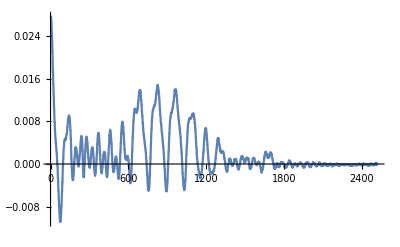

```mathematica
data=preprocess[rawdata];
ListLinePlot[{x},PlotRange->All]
```

```mathematica
ArcSin[{1,Mean[{}],1}]
```

{π/2,ArcSin[Mean[{}]],π/2}

```mathematica
Mean[θ2[[-100;;All]]]
```

0.0144187

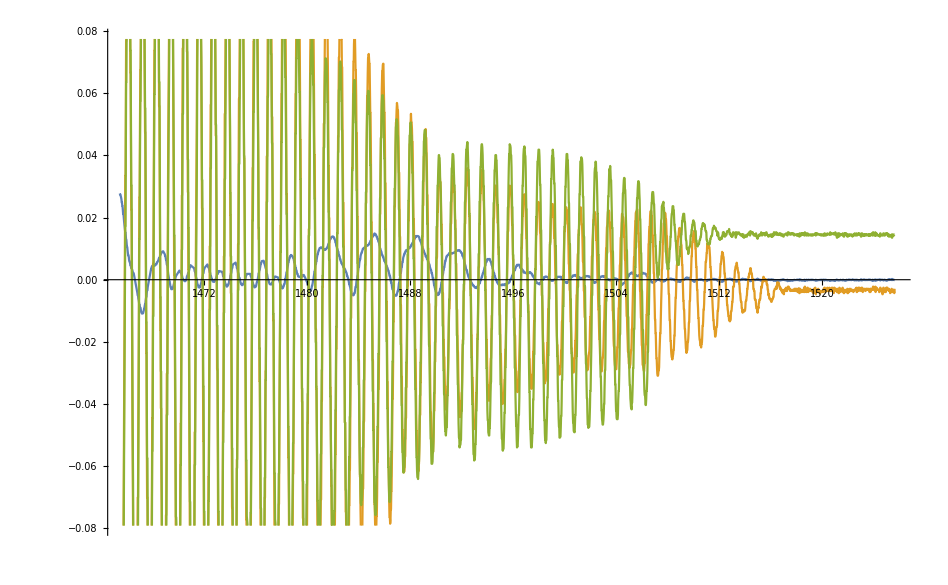

```mathematica
ListLinePlot[Transpose@{data[[All,1]],#}&/@Transpose[data][[2;;All]]]
```

# Process all the files

```mathematica
filenames=FileNames["data/raw/*.tsv"]
```

{data/raw/death1.tsv,data/raw/death2.tsv,data/raw/death3.tsv,data/raw/final_heavy_death1.tsv,data/raw/final_heavy_death2.tsv,data/raw/final_heavy_singlestart_death.tsv,data/raw/final_heavy_singlestart_stabilizes1.tsv,data/raw/final_light_dies.tsv,data/raw/final_light_rocking.tsv,data/raw/final_light_singlestart_stabilizes1.tsv,data/raw/final_light_stabilizes1.tsv,data/raw/final_light_stable1.tsv,data/raw/final_medium_death1.tsv,data/raw/final_medium_rocking1.tsv,data/raw/final_medium_singlestart_death1.tsv,data/raw/final_medium_singlestart_stabilizes2.tsv,data/raw/final_medium_singlestart_stabilizes3.tsv,data/raw/final_medium_stabilizes1.tsv,data/raw/rocking1.tsv,data/raw/stabilizing1.tsv,data/raw/stablestart1.tsv}

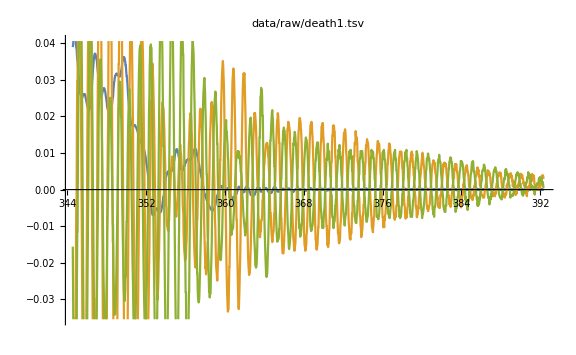
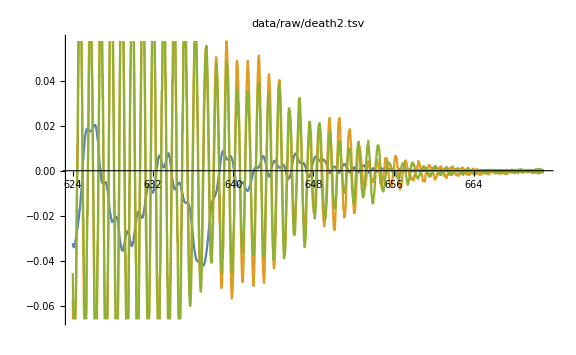
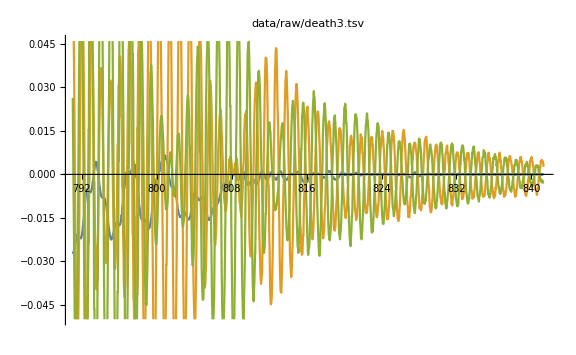
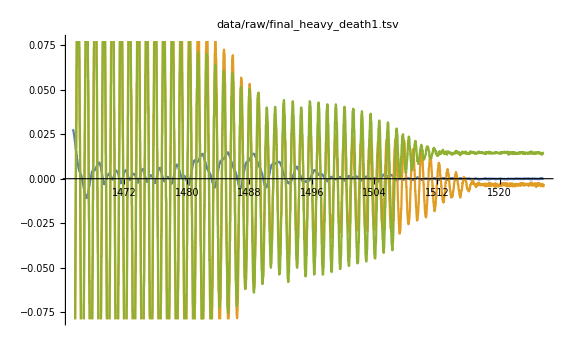
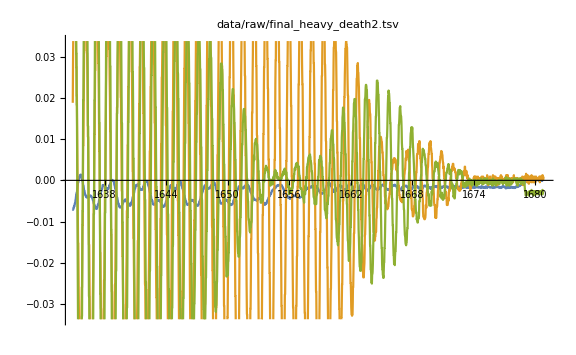
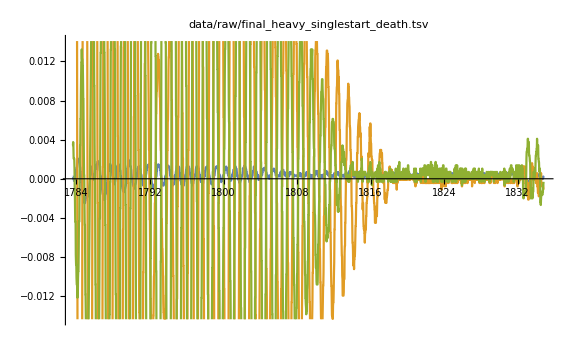
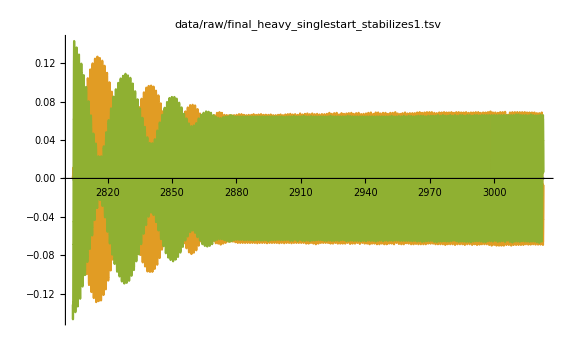
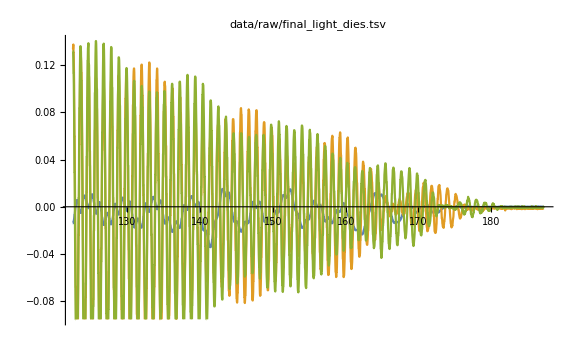

```mathematica
Column@Module[{data},
Table[data=preprocess[Import[f]];Export[StringReplace[f,"/raw/"->"/cleaned/"],data];
ListLinePlot[
Transpose@{data[[All,1]],#}&/@Transpose[data][[2;;All]],
PlotLabel->f,ImageSize->Large],
{f,filenames}]
]
```